# Tarea 2, Mat1620L/ Agustín Bustamante

## Preguntas

### 1)

#### Ejercicio 1

Partimos definiendo la funciones necesaria para el primer ejercicio, siendo esta la funcion “f”. Definimos el gradiente simbólico de la funcion y luego se define nuevamente pero como funcion numérica, para despues definir la funcion SDstep.

```mathematica
ClearAll["Global`*"]
f[x_,y_,z_] := ((y-x+z)^2) + ((3*x-y^2)^2) + ((6-x-z-y^2)^2)
gradex = Grad[f[x,y,z], {x,y,z}]//Simplify
gradf[li_List] := Evaluate[gradex/. Thread[{x,y,z}->li]]//N
SDstep[x_List] := Module[{g, phi,sol,tStar}, g = N[gradf[x]];
 phi[t_?NumericQ] := N[f @@ (x - t*g)];
 Quiet[sol= FindMinimum[phi[t],{t,0}];];
If[MatchQ[sol, {_,{Rule[_,_]}}],tStar=t/. Last[sol];
 N[x-tStar*g], N[x-0.1*g]]];
```

{22 x-2 (6+y+2 y^2),2 (4 y^3-x (1+4 y)+z+y (-11+2 z)),2 (-6+y+y^2+2 z)}

Ahora, definimos el punto inicial x0 y mediante NestList y la funcion definida SDstep 20 veces generando una secuencia completa de puntos. Para finalmente extraer el ultimo punto generado mediante el comando Last.

```mathematica
x0 = {2,1,1.5}
SDsecuencia := NestList[SDstep, x0, 20]
ReFinal = Last[SDsecuencia]
```

{2,1,1.5}

{1.61196,2.19552,-0.408437}

Evaluemos la funcion en el punto, y calculamos su gradiente en el mismo punto

```mathematica
fFinal = f @@ ReFinal
gradFin = gradf[ReFinal]
```

0.0314801

{-0.209223,0.423061,0.397947}

Comparamos el método utilizado con el incorporado de manera local en el mismo punto de inicio

```mathematica
SolOpti = FindMinimum[f[x, y, z],{x, x0[[1]]}, {y, x0[[2]]}, {z,x0[[3]]}]
```

{8.42929×10^-25,{x→1.64419,y→2.22094,z→-0.57675}}

Podemos ver una semejanza clara entre los puntos, pero una diferencia notable en el valor final producido por ambos métodos, de esto podemos deducir que si bien el método converge al punto esperado, no logra llegar con solamente 20 pasos.

#### Ejercicio 2

Repetimos el mismo método anterior

```mathematica
ClearAll["Global`*"]
f[a_,b_,c_] := (a + b*Sin[c] - 0.92)^2 + (2*a + b*Sin[2*c] - 1.16)^2 + (3*a + b*Sin[3*c] - 0.79)^2
gradex := Grad[f[a,b,c], {a,b,c}]//Simplify
gradf[li_List] := Evaluate[gradex/. Thread[{a,b,c}->li]]//N
SDstep[x_List] := Module[{g, phi,sol,tStar}, g = N[gradf[x]];
 phi[t_?NumericQ] := N[f @@ (x - t*g)];
 Quiet[sol= FindMinimum[phi[t],{t,0}];];
If[MatchQ[sol, {_,{Rule[_,_]}}],tStar=t/. Last[sol];
 N[x-tStar*g], N[x-0.1*g]]];
```

```mathematica
x0 = {0.3,0.7,1}
SDsecuencia := NestList[SDstep, x0, 30]
```

{0.3,0.7,1}

```mathematica
ReFinal = Last[SDsecuencia]
```

{0.275847,0.728419,1.06571}

```mathematica
fFinal = f @@ ReFinal
```

0.000127229

```mathematica
gradFin = gradf[ReFinal]
```

{0.00367643,0.00319521,-0.00541207}

```mathematica
SolOpti = FindMinimum[f[a, b, c],{a, x0[[1]]}, {b, x0[[2]]}, {c,x0[[3]]}]
```

{7.20625×10^-30,{a→0.303467,b→0.689814,c→1.10568}}

Podemos ver que para ambos métodos nuevamente se asemejan bastante los puntos, pero podemos notar una diferencia nuevamente entre ambos al evaluar el punto pero esta es muy leve, ya que ambos representan números muy pequeños, de esto podemos concluir que la aproximación con 30 pasos cumple de manera aceptable con el valor requerido

#### Ejercicio 3

Definimos la funcion y el gradiente de la misma forma que en las anteriores

```mathematica
ClearAll["Global`*"]
f[x_,y_] := (x + 3*y - 5)^2 + (x-2*y)^2
gradex = Grad[f[x,y], {x,y}]//Simplify
gradf[li_List] := Evaluate[gradex/. Thread[{x,y}->li]]//N
SDstep[x_List] := Module[{g, phi,sol,tStar}, g = N[gradf[x]];
 phi[t_?NumericQ] := N[f @@ (x - t*g)];
 Quiet[sol= FindMinimum[phi[t],{t,0}];];
If[MatchQ[sol, {_,{Rule[_,_]}}],tStar=t/. Last[sol];
 N[x-tStar*g], N[x-0.1*g]]];
```

{2 (-5+2 x+y),2 (-15+x+13 y)}

Se generan los 12 pasos de la aproximacion

```mathematica
x0 = {0,1}
SDsecuencia := NestList[SDstep, x0, 12]
```

{0,1}

Generamos las gráficas mediante ContourPlot y ListLinePlot

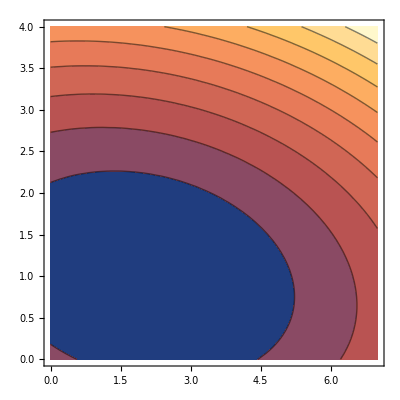

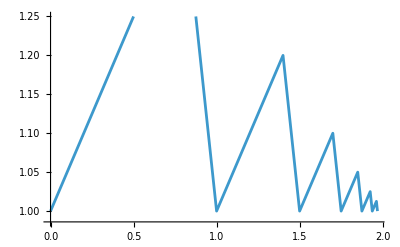

```mathematica
graf1 = ContourPlot[f[x,y], {x, 0,7}, {y,0,4}]
graf2 = ListLinePlot[SDsecuencia]
```

El primer grafico nos muestra las curvas de nivel elípticas generadas de la funcion f. El segundo gráfico muestra la trayectoria que sigue la secuencia, la cual inicia en 0.1 y se acerca cada vez mas al mínimo esperado. La gráfica concuerda claramente con lo esperado teóricamente, ya que si tiene un movimiento de tipo “Zig-Zag”, este movimiento concuerda con las características del vector gradiente, ya que este es siempre perpendicular a las curvas de nivel. Al ser las curvas elípticas el vector no puede apuntar directamente al mínimo, produciendo este movimiento.

### 2)

#### Adicional 1 (Justificado)

Definimos las funciones ncesarias, el gradiente y la Hessiana

```mathematica
ClearAll["Global`*"];
f[x_,y_,z_] := (y-x+z)^2 + (3*x - y^2)^2 + (6 - x - y^2 -z)^2;
gradex := Grad[f[x,y,z], {x,y,z}]//Simplify;
gradf[li_List] := Evaluate[gradex/. Thread[{x,y,z}->li]]//N;
hessexp = D[f[x,y,z],{{x,y,z},2}] // Simplify;
hessf[li_List] := Evaluate[hessexp /. Thread[{x,y,z}->li]] // N;
SDstep[x_List] := Module[{g, phi,sol,tStar}, g = N[gradf[x]];
 phi[t_?NumericQ] := N[f @@ (x - t*g)];
 Quiet[sol= FindMinimum[phi[t],{t,0}];];
If[MatchQ[sol, {_,{Rule[_,_]}}],tStar=t/. Last[sol];
 N[x-tStar*g], N[x-0.1*g]]];
SDstepMejorado[x_List] := Module[{g, H, tStar}, g =N[gradf[x]];
h=N[hessf[x]];
tStar = (g.g) / (g.h.g);
N[x-tStar*g]]
```

Se ejecutan ambos métodos en las coordenadas dadas, con 30 pasos y utilizamos la funcion Timing para comparar la eficiencia de ambos metodos

```mathematica
x0 = {2.0, 1.0, 1.5};
```

```mathematica
{TME, ReE} = Timing[NestList[SDstep, x0, 30]];
ReFinalE = Last[ReE];
fiFinME = f @@ ReFinalE
{TMM, ReM} = Timing[NestList[SDstepMejorado, x0, 30]];
ReFinalM := Last[ReM];
fFinMM = f @@ ReFinalM
print[TME,TMM]
```

0.0108678

0.00120291

print[0.03125,0.015625]

Podemos notar que efectivamente el método mejorado resulta mas rápido para la aproximación, Con tiempos variables pero siempre ejecuta de manera mas rápida.
Notamos también la diferencia entre los valores, la cual se debe a distintos métodos de aproximación, podemos predecir que con pasos que tiendan a infinito los resultados serán los mismos.
Realizamos el gráfico de convergencia. con las funciones Map y ListPlot

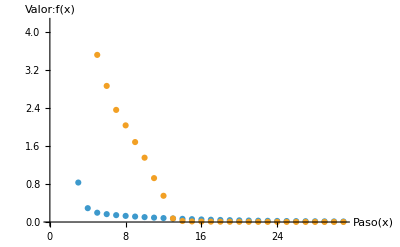

```mathematica
GrafE = Map[f @@ # &, ReE];
GrafM = Map[f @@ # &, ReM];
ListPlot[{GrafE,GrafM}, AxesLabel->{"Paso(x)", "Valor:f(x)"}]
```

Podemos apreciar que la funcion nueva, no solamente es mas rápida, si no que también resulta mas precisa para el calculo ya que se aproxima mucho mas al valor esperado utilizando la misma cantidad de pasos que la original

#### Adicional 2

Realizamos el mismo procedimiento que con anterioridad

```mathematica
ClearAll["Global`*"];
f[x_,y_,z_] := Sin[(x-y+z)^2]+Sin[x+y-2]^2 + (x^2)*(y^4);
gradex := Grad[f[x,y,z], {x,y,z}]//Simplify;
gradf[li_List] := Evaluate[gradex/. Thread[{x,y,z}->li]]//N;
hessexp = D[f[x,y,z],{{x,y,z},2}] // Simplify;
hessf[li_List] := Evaluate[hessexp /. Thread[{x,y,z}->li]] // N;
SDstep[x_List] := Module[{g, phi,sol,tStar}, g = N[gradf[x]];
 phi[t_?NumericQ] := N[f @@ (x - t*g)];
 Quiet[sol= FindMinimum[phi[t],{t,0}];];
If[MatchQ[sol, {_,{Rule[_,_]}}],tStar=t/. Last[sol];
 N[x-tStar*g], N[x-0.1*g]]];
SDstepMejorado[x_List] := Module[{g, H, tStar}, g =N[gradf[x]];
h=N[hessf[x]];
tStar = (g.g) / (g.h.g);
N[x-tStar*g]]
x0 = {0.8, 1.3,0.2};
SDsecuenciaE = NestList[SDstep,x0,20];
SDsecuenciaM = NestList[SDstepMejorado,x0,20];
f@@Last[SDsecuenciaE]
f@@Last[SDsecuenciaM]
```

0.0085933

0.0523284

Apreciamos que la versión mejorada es mas precisa.

#### Adicional 3

Realizamos el mismo procedimiento que con anterioridad.

```mathematica
ClearAll["Global`*"];
f[x_,y_,z_] := E^((x-y)^2) + Sin[(E^y)*(x^2+z-2)]^2+(z-1)^2;
gradex := Grad[f[x,y,z], {x,y,z}]//Simplify;
gradf[li_List] := Evaluate[gradex/. Thread[{x,y,z}->li]]//N;
hessexp = D[f[x,y,z],{{x,y,z},2}] // Simplify;
hessf[li_List] := Evaluate[hessexp /. Thread[{x,y,z}->li]] // N;
SDstep[x_List] := Module[{g, phi,sol,tStar}, g = N[gradf[x]];
 phi[t_?NumericQ] := N[f @@ (x - t*g)];
 Quiet[sol= FindMinimum[phi[t],{t,0}];];
If[MatchQ[sol, {_,{Rule[_,_]}}],tStar=t/. Last[sol];
 N[x-tStar*g], N[x-0.1*g]]];
SDstepMejorado[x_List] := Module[{g, H, tStar}, g =N[gradf[x]];
h=N[hessf[x]];
tStar = (g.g) / (g.h.g);
N[x-tStar*g]]
x0 = {0.8, 1.3,1.2};
SDsecuenciaE = NestList[SDstep,x0,30];
SDsecuenciaM = NestList[SDstepMejorado,x0,30];
f@@Last[SDsecuenciaE]
f@@Last[SDsecuenciaM]
```

1.

1.4054

#### Adicional 4

Realizamos el mismo procedimiento que con anterioridad

```mathematica
ClearAll["Global`*"];
f[x_,y_,z_] := (y^2-z)^2 + (x^2-y)^2 + ArcTan[(1.3-y)^2+(0.8-z)^2];
gradex := Grad[f[x,y,z], {x,y,z}]//Simplify;
gradf[li_List] := Evaluate[gradex/. Thread[{x,y,z}->li]]//N;
hessexp = D[f[x,y,z],{{x,y,z},2}] // Simplify;
hessf[li_List] := Evaluate[hessexp /. Thread[{x,y,z}->li]] // N;
SDstep[x_List] := Module[{g, phi,sol,tStar}, g = N[gradf[x]];
 phi[t_?NumericQ] := N[f @@ (x - t*g)];
 Quiet[sol= FindMinimum[phi[t],{t,0}];];
If[MatchQ[sol, {_,{Rule[_,_]}}],tStar=t/. Last[sol];
 N[x-tStar*g], N[x-0.1*g]]];
SDstepMejorado[x_List] := Module[{g, H, tStar}, g =N[gradf[x]];
h=N[hessf[x]];
tStar = (g.g) / (g.h.g);
N[x-tStar*g]]
x0 = {1.0, 1.0,1.0};
SDsecuenciaE = NestList[SDstep,x0,30];
SDsecuenciaM = NestList[SDstepMejorado,x0,30];
f@@Last[SDsecuenciaE]
f@@Last[SDsecuenciaM]
```

0.106693

0.106693

Notar que los valores coinciden, por lo que para ambos casos con 30 pasos fue suficiente par allegar a una aproximación exacta.